```mathematica
ClearAll["Global`*"]
```

```mathematica
(*This is the code to perform calculations for LESCO. The calculations can be found in "One Note/Effect of stress on transition temperature/ BAck Calculations"*)
```

```mathematica
(*Extracting the Stress vs Strain data for LESCO*)
(*-Graphics- The units are in K and Kbar=10^8 Pa*)
```

```mathematica
P110={{-0.0846182853784988,9.89492119089317},{-0.5595319342875719,11.120840630472856},{-0.9816424405490377,12.276707530647986},{-1.540952279599396,13.782837127845884},{-2.089749610754962,15.183887915936953},{-2.5224466566569577,16.30472854640981},{-2.9234581153831027,17.390542907180386}};
P100={{-0.05341390454994477,8.949211908931698},{-0.4548510458140832,9.229422066549912},{-0.7822934572131212,9.544658493870402},{-1.1625760271326349,9.859894921190893},{-1.9759443096192686,10.560420315236426},{-2.979444623097442,11.436077057793344}};
P001={{-0.011308349161474829,8.633975481611207},{-0.2544471101014002,8.493870402802102},{-0.48701783933723075,8.353765323992993},{-0.8993006313519817,8.108581436077058},{-1.4384738355616116,7.723292469352012},{-1.988196563538903,7.373029772329247},{-2.728217893935643,6.882661996497372},{-2.9713751628120035,6.70753064798599},{-3.425967097516003,6.392294220665498},{-3.7325510645533684,6.182136602451838}};
P110[[1,2]]
Sclng:=10^8(*to convert Kbar to Pascal*)
P110[[;;,1]]=Sclng*P110[[;;,1]];
P110
P100[[;;,1]]=Sclng*P100[[;;,1]];
P100
P001[[;;,1]]=Sclng*P001[[;;,1]];
P001
```

9.89492

{{-8.46183×10^6,9.89492},{-5.59532×10^7,11.1208},{-9.81642×10^7,12.2767},{-1.54095×10^8,13.7828},{-2.08975×10^8,15.1839},{-2.52245×10^8,16.3047},{-2.92346×10^8,17.3905}}

{{-5.34139×10^6,8.94921},{-4.54851×10^7,9.22942},{-7.82293×10^7,9.54466},{-1.16258×10^8,9.85989},{-1.97594×10^8,10.5604},{-2.97944×10^8,11.4361}}

{{-1.13083×10^6,8.63398},{-2.54447×10^7,8.49387},{-4.87018×10^7,8.35377},{-8.99301×10^7,8.10858},{-1.43847×10^8,7.72329},{-1.9882×10^8,7.37303},{-2.72822×10^8,6.88266},{-2.97138×10^8,6.70753},{-3.42597×10^8,6.39229},{-3.73255×10^8,6.18214}}

```mathematica
(*Collecting Data for the lattice parameters*)
(*-Graphics-*)
a0VsT:={{139.77619532044764,5.3445833333333335},{129.8067141403866,5.3445833333333335},{119.83723296032555,5.3445833333333335},{109.8677517802645,5.344513888888889},{99.89827060020345,5.344305555555556},{89.72533062054934,5.344166666666666},{79.7558494404883,5.344236111111111},{69.78636826042727,5.344027777777778},{59.81688708036623,5.3438888888888885},{49.64394710071211,5.3438888888888885},{39.87792472024415,5.343819444444445},{29.70498474059002,5.343819444444445},{19.73550356052899,5.343819444444445},{9.766022380467952,5.3438888888888885}}
aVsT:={{149.74567650050864,5.323472222222223},{159.7151576805697,5.323819444444444},{169.88809766022382,5.324305555555555},{179.85757884028487,5.324722222222222},{190.03051881993895,5.325347222222223},{200,5.325972222222222}}
bVsT:={{149.94913530010172,5.362777777777778},{159.7151576805697,5.362847222222222},{169.88809766022382,5.362777777777778},{179.85757884028487,5.362638888888889},{190.03051881993895,5.3625},{199.79654120040692,5.362361111111111}}
c0VsT:={{139.97965412004078,13.12918216976042},{130.0101729399796,13.125449400949748},{120.04069175991862,13.123659951977132},{109.86775178026454,13.122032281580388},{100.10172939979657,13.120566883991415},{89.92878942014244,13.11893921359467},{79.95930824008138,13.117797537901408},{69.98982706002033,13.116493918888306},{60.020345879959336,13.115514186514881},{50.050864699898284,13.114858340781133},{40.081383519837175,13.114202495047383},{30.11190233977618,13.11387053595331},{19.93896236012216,13.113700355435109},{9.969481180061052,13.113692282980711}}
cVsT:={{150.1525940996949,13.126923200481052},{160.12207527975585,13.128874592773505},{170.0915564598169,13.13066404174612},{180.06103763987795,13.132615434038573},{190.03051881993906,13.134728769650865},{200,13.136842105263156}}
```

```mathematica
(*Setting up the Canonical basis vectors*)
e1:={1,0,0}
e2:={0,1,0}
e3:={0,0,1}
(*Setting up the lattice vectors for the Tetragonal and Orthorhombic Lattices and dual Cubic lattice *)
Subscript[a, 0]=a0VsT[[1,2]];
Subscript[c, 0]=c0VsT[[1,2]];
a=aVsT[[1,2]];
b=bVsT[[1,2]];
c=cVsT[[1,2]];
Print["a_0=",Subscript[a, 0]]
Print["c_0=",Subscript[c, 0]]
Print["a=",a]
Print["b=",b]
Print["c=",c]
Print["The angle of the orthorhombic phase is", ArcTan[b,a]]
```

a_0=5.34458

c_0=13.1292

a=5.32347

b=5.36278

c=13.1269

The angle of the orthorhombic phase is0.78172

```mathematica
(*Using the characterization of the Rotation matrix to determine the Symmetries if the cubic, Tetragonal and Orthorhombic phase.*)
Qq[ux_,uy_,uz_,t_]:={{Cos[t]+ux^2*(1-Cos[t]) , ux*uy*(1-Cos[t])-uz*Sin[t] , ux*uz*(1-Cos[t])+uy*Sin[t]},{ ux*uy*(1-Cos[t])+uz*Sin[t] ,Cos[t]+uy^2*(1-Cos[t]) , uy*uz*(1-Cos[t])-ux*Sin[t]},{ ux*uz*(1-Cos[t])-uy*Sin[t] , uy*uz*(1-Cos[t])+ux*Sin[t] ,Cos[t]+uz^2*(1-Cos[t])}}
```

```mathematica
Qq[-1/Sqrt[3],1/Sqrt[3],-1/Sqrt[3],4/3*Pi]//MatrixForm
```

(0 | -1 | 0
0 | 0 | -1
1 | 0 | 0)

```mathematica
(*Intutitively checking the differerent deformations*)
θ=ArcTan[b,a];
Print["Checking for σ_100, if we have (F_S)_11<(F_N)_11 with rotation of variant II ---> ",a/Subscript[a, 0]*Cos[θ]-1," Since this is -ve, this is not the variant that we get"]
Print["Checking for σ_100, if we have (F_S)_11<(F_N)_11 with rotation of variant I ---> ",b/Subscript[a, 0]*Sin[θ]-1," Since this is -ve, this is not the variant that we get"]
Print["Checking for σ_001, if we have (F_S)_33>(F_N)_33 with variant I or II ---> ",1-c/Subscript[c, 0]," Since this is +ve, this is the right choice of minimizer"]
```

Checking for σ_100, if we have (F_S)_11<(F_N)_11 with rotation of variant II ---> -0.293101 Since this is -ve, this is not the variant that we get

Checking for σ_100, if we have (F_S)_11<(F_N)_11 with rotation of variant I ---> -0.293101 Since this is -ve, this is not the variant that we get

Checking for σ_001, if we have (F_S)_33>(F_N)_33 with variant I or II ---> 0.000172057 Since this is +ve, this is the right choice of minimizer

9.7-2.642×10^-8 P

-3.78501×10^7

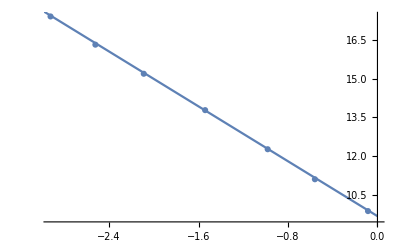

8.9-8.35454×10^-9 P

-1.19695×10^8

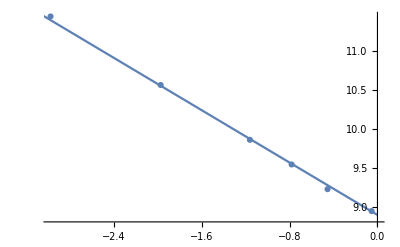

8.65+6.50092×10^-9 P

1.53824×10^8

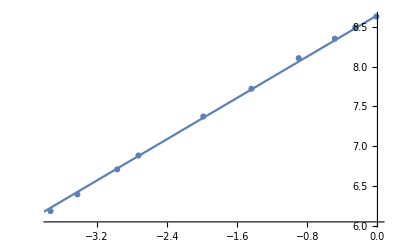

```mathematica
(*Plotting the Stress vs Transition Temperature Data &Computing Slopes*)
dP110bdT=Table[((P110[[i,1]]-P110[[i+1,1]])/(P110[[i,2]]-P110[[i+1,2]])),{i,1,Length[P110]-1}];
T110[P_]:=9.7+(Total[dP110bdT]/Length[dP110bdT])^-1*P
T110[P]
Total[dP110bdT]/Length[dP110bdT]
p1=ListPlot[P110, PlotMarkers->Automatic];
p2 = Plot[T110[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP100bdT=Table[((P100[[i,1]]-P100[[i+1,1]])/(P100[[i,2]]-P100[[i+1,2]])),{i,1,Length[P100]-1}];
T100[P_]:=8.9+(Total[dP100bdT]/Length[dP100bdT])^-1*P
T100[P]
Total[dP100bdT]/Length[dP100bdT]
p1=ListPlot[P100, PlotMarkers->Automatic];
p2 = Plot[T100[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
dP001bdT=Table[((P001[[i,1]]-P001[[i+1,1]])/(P001[[i,2]]-P001[[i+1,2]])),{i,1,Length[P001]-1}];
T001[P_]:=8.65+(Total[dP001bdT]/Length[dP001bdT])^-1*P
T001[P]
Total[dP001bdT]/Length[dP001bdT]
p1=ListPlot[P001, PlotMarkers->Automatic];
p2 = Plot[T001[P],{P,-4*10^8,0}];
Show[p1,p2]
Clear[p1,p2]
```

```mathematica
(*Claussius Clayperon*)
K1=Total[dP100bdT]/Length[dP100bdT]
K2=Total[dP110bdT]/Length[dP110bdT]
K3=Total[dP001bdT]/Length[dP001bdT]
Subscript[Δη, 100]=-K1*(a/Subscript[a, 0]-1);
Subscript[Δη, 001]=-K3*(c/Subscript[c, 0]-1);
Subscript[F, N11]=1+Subscript[Δη, 001]/K1;
Print["--------------------------------------------------"]
Print["The Δη of Cl-Cp for σ_100 is= ",Subscript[Δη, 100]]
Print["The Δη of Cl-Cp for σ_001 is= ",Subscript[Δη, 001]]
Print["c/c_0 calculated with Δη_100 plugged into σ_001= ",1+Subscript[Δη, 100]/K3, ". The corresponding value of c given c_0 is -->",(1+Subscript[Δη, 100]/K3)*Subscript[c, 0]]
Print["(F_N)_11 calculated with Δη_100 plugged into σ_001= ",Subscript[F, N11]]
Print["New b calculated from (F_N)_11 above is= ",Subscript[a, 0]*Subscript[F, N11]]
Print["New 'Sine of Angle of Rotation' calculated from (F_N)_11 using Variant I is = ",Subscript[a, 0]/b*Subscript[F, N11]," This gives us sin^-1(...) = ",ArcSin[Subscript[a, 0]/b*Subscript[F, N11]]]
Print["New 'Cosine of Angle of Rotation' calculated from (F_N)_11 using Variant II is = ",Subscript[a, 0]/a*Subscript[F, N11]," Thus this canot be the ans."]
Print["Keeping the dimension of a the same, the new b calculated from (F_N)_11 using Variant I, and allowing for rotation that make the edges flat is = ",(Subscript[F, N11]*Subscript[a, 0])/Sqrt[1-Subscript[a, 0]^2/a^2*Subscript[F, N11]^2]]
```

-1.19695×10^8

-3.78501×10^7

1.53824×10^8

--------------------------------------------------

The Δη of Cl-Cp for σ_100 is= -472797.

The Δη of Cl-Cp for σ_001 is= 26466.6

c/c_0 calculated with Δη_100 plugged into σ_001= 0.996926. The corresponding value of c given c_0 is -->13.0888

(F_N)_11 calculated with Δη_100 plugged into σ_001= 0.999779

New b calculated from (F_N)_11 above is= 5.3434

New 'Sine of Angle of Rotation' calculated from (F_N)_11 using Variant I is = 0.996387 This gives us sin^-1(...) = 1.48576

New 'Cosine of Angle of Rotation' calculated from (F_N)_11 using Variant II is = 1.00374 Thus this canot be the ans.

Keeping the dimension of a the same, the new b calculated from (F_N)_11 using Variant I, and allowing for rotation that make the edges flat is = 0.-61.6947 ⅈ

```mathematica
A={{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}
Qq[0,0,1,θ-Pi/4]//MatrixForm
Temp=Qq[0,0,1,θ-Pi/4].{{α,0,0},{0,β,0},{0,0,γ}}
Subscript[Δη, 001]=-K2*(Tr[A.Temp]-Tr[A])/.α->a/Subscript[a, 0]/.β->b/Subscript[a, 0]
```

{{1/2,1/2,0},{1/2,1/2,0},{0,0,0}}

(0.999993 | 0.00367812 | 0.
-0.00367812 | 0.999993 | 0.
0. | 0. | 1.)

{{0.+0.999993 α,0.+0.00367812 β,0.},{0.-0.00367812 α,0.+0.999993 β,0.},{0.,0.,0.+1. γ}}

-10071.9

```mathematica
2/K2^2-1/K1^2
2/K2-1/K1
```

1.32623×10^-15

-4.44854×10^-8